```mathematica
L=4;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

25

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

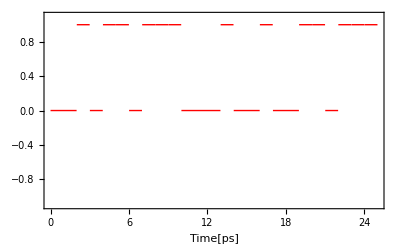

1/(f π)ⅇ^(-49 ⅈ f π) (1+ⅇ^(2 ⅈ f π)+ⅇ^(4 ⅈ f π)+ⅇ^(8 ⅈ f π)+ⅇ^(10 ⅈ f π)+ⅇ^(16 ⅈ f π)+ⅇ^(22 ⅈ f π)+ⅇ^(30 ⅈ f π)+ⅇ^(32 ⅈ f π)+ⅇ^(34 ⅈ f π)+ⅇ^(38 ⅈ f π)+ⅇ^(40 ⅈ f π)+ⅇ^(44 ⅈ f π)) Sin[f π]

```mathematica
bit=25
bit=25;
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i<t<(i+1),1,0],If[i<t<(i+1),0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[Evaluate[signal[t]],{t,0,bit},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
∫_0^bit signal[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

```mathematica
{0,1,1,0,0,0,0,0,0,1,1,1,1,0,0,1,1,1,1,1,1,0,0,1,1}
```

{0,1,1,0,0,0,0,0,0,1,1,1,1,0,0,1,1,1,1,1,1,0,0,1,1}

Cos[1216.42 t]

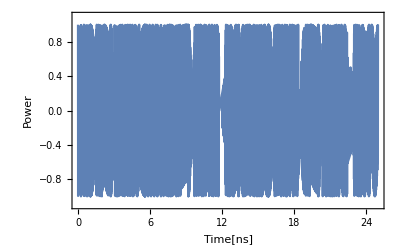

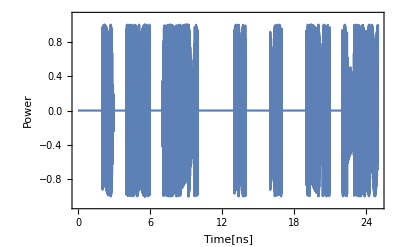

-Graphics-

0.+(18.1111 Cos[0.-2563.54 f] Cos[0.+2400.18 f])/(-37481.+1. f^2)+(9.28311×10^-9 Cos[0.-2563.54 f] Cos[0.+2406.46 f])/(-37481.+1. f^2)+(9.32464×10^-9 Cos[0.-2563.54 f] Cos[0.+2406.46 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Cos[0.+2412.74 f])/(-37481.+1. f^2)-(18.1111 Cos[0.-2563.54 f] Cos[0.+2412.74 f])/(-37481.+1. f^2)-(29.3043 Cos[0.-2563.54 f] Cos[0.+2419.03 f])/(-37481.+1. f^2)+(29.3043 Cos[0.-2563.54 f] Cos[0.+2419.03 f])/(-37481.+1. f^2)+(29.3043 Cos[0.-2563.54 f] Cos[0.+2425.31 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Cos[0.+2431.59 f])/(-37481.+1. f^2)+(7.51616×10^-9 Cos[0.-2563.54 f] Cos[0.+2437.88 f])/(-37481.+1. f^2)+(7.50455×10^-9 Cos[0.-2563.54 f] Cos[0.+2437.88 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Cos[0.+2444.16 f])/(-37481.+1. f^2)-(29.3043 Cos[0.-2563.54 f] Cos[0.+2456.73 f])/(-37481.+1. f^2)-(18.1111 Cos[0.-2563.54 f] Cos[0.+2463.01 f])/(-37481.+1. f^2)-(18.1111 Cos[0.-2563.54 f] Cos[0.+2475.58 f])/(-37481.+1. f^2)-(29.3043 Cos[0.-2563.54 f] Cos[0.+2481.86 f])/(-37481.+1. f^2)+(3.75227×10^-9 Cos[0.-2563.54 f] Cos[0.+2500.71 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Cos[0.+2506.99 f])/(-37481.+1. f^2)-(18.1111 Cos[0.-2563.54 f] Cos[0.+2506.99 f])/(-37481.+1. f^2)-(29.3043 Cos[0.-2563.54 f] Cos[0.+2513.27 f])/(-37481.+1. f^2)+(29.3043 Cos[0.-2563.54 f] Cos[0.+2513.27 f])/(-37481.+1. f^2)+(29.3043 Cos[0.-2563.54 f] Cos[0.+2519.56 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Cos[0.+2525.84 f])/(-37481.+1. f^2)+(1.87904×10^-9 Cos[0.-2563.54 f] Cos[0.+2532.12 f])/(-37481.+1. f^2)+(1.87614×10^-9 Cos[0.-2563.54 f] Cos[0.+2532.12 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Cos[0.+2538.41 f])/(-37481.+1. f^2)+(29.3043 Cos[0.-2563.54 f] Cos[0.+2544.69 f])/(-37481.+1. f^2)+(29.3043 Cos[0.-2563.54 f] Cos[0.+2550.97 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.+2400.18 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.159155 f Cos[0.+2406.46 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.159155 f Cos[0.+2406.46 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.+2412.74 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.+2412.74 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.+2419.03 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.+2419.03 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.+2425.31 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.+2431.59 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.159155 f Cos[0.+2437.88 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.159155 f Cos[0.+2437.88 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.+2444.16 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.+2456.73 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.+2463.01 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.+2475.58 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.+2481.86 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.159155 f Cos[0.+2500.71 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.+2506.99 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.+2506.99 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.+2513.27 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.+2513.27 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.+2519.56 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.+2525.84 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.159155 f Cos[0.+2532.12 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.159155 f Cos[0.+2532.12 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.+2538.41 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.+2544.69 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.+2550.97 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.-2563.54 f] Sin[0.+2400.18 f])/(-37481.+1. f^2)-(18.1111 Sin[0.-2563.54 f] Sin[0.+2400.18 f])/(-37481.+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2406.46 f])/(-37481.+1. f^2)-(9.28311×10^-9 Sin[0.-2563.54 f] Sin[0.+2406.46 f])/(-37481.+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2406.46 f])/(-37481.+1. f^2)-(9.32464×10^-9 Sin[0.-2563.54 f] Sin[0.+2406.46 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.-2563.54 f] Sin[0.+2412.74 f])/(-37481.+1. f^2)-(18.1111 Sin[0.-2563.54 f] Sin[0.+2412.74 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.-2563.54 f] Sin[0.+2412.74 f])/(-37481.+1. f^2)+(18.1111 Sin[0.-2563.54 f] Sin[0.+2412.74 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.-2563.54 f] Sin[0.+2419.03 f])/(-37481.+1. f^2)+(29.3043 Sin[0.-2563.54 f] Sin[0.+2419.03 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.-2563.54 f] Sin[0.+2419.03 f])/(-37481.+1. f^2)-(29.3043 Sin[0.-2563.54 f] Sin[0.+2419.03 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.-2563.54 f] Sin[0.+2425.31 f])/(-37481.+1. f^2)-(29.3043 Sin[0.-2563.54 f] Sin[0.+2425.31 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.-2563.54 f] Sin[0.+2431.59 f])/(-37481.+1. f^2)-(18.1111 Sin[0.-2563.54 f] Sin[0.+2431.59 f])/(-37481.+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2437.88 f])/(-37481.+1. f^2)-(7.51616×10^-9 Sin[0.-2563.54 f] Sin[0.+2437.88 f])/(-37481.+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2437.88 f])/(-37481.+1. f^2)-(7.50455×10^-9 Sin[0.-2563.54 f] Sin[0.+2437.88 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.-2563.54 f] Sin[0.+2444.16 f])/(-37481.+1. f^2)-(18.1111 Sin[0.-2563.54 f] Sin[0.+2444.16 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.-2563.54 f] Sin[0.+2456.73 f])/(-37481.+1. f^2)+(29.3043 Sin[0.-2563.54 f] Sin[0.+2456.73 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.-2563.54 f] Sin[0.+2463.01 f])/(-37481.+1. f^2)+(18.1111 Sin[0.-2563.54 f] Sin[0.+2463.01 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.-2563.54 f] Sin[0.+2475.58 f])/(-37481.+1. f^2)+(18.1111 Sin[0.-2563.54 f] Sin[0.+2475.58 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.-2563.54 f] Sin[0.+2481.86 f])/(-37481.+1. f^2)+(29.3043 Sin[0.-2563.54 f] Sin[0.+2481.86 f])/(-37481.+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2500.71 f])/(-37481.+1. f^2)-(3.75227×10^-9 Sin[0.-2563.54 f] Sin[0.+2500.71 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.-2563.54 f] Sin[0.+2506.99 f])/(-37481.+1. f^2)-(18.1111 Sin[0.-2563.54 f] Sin[0.+2506.99 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.-2563.54 f] Sin[0.+2506.99 f])/(-37481.+1. f^2)+(18.1111 Sin[0.-2563.54 f] Sin[0.+2506.99 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.-2563.54 f] Sin[0.+2513.27 f])/(-37481.+1. f^2)+(29.3043 Sin[0.-2563.54 f] Sin[0.+2513.27 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.-2563.54 f] Sin[0.+2513.27 f])/(-37481.+1. f^2)-(29.3043 Sin[0.-2563.54 f] Sin[0.+2513.27 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.-2563.54 f] Sin[0.+2519.56 f])/(-37481.+1. f^2)-(29.3043 Sin[0.-2563.54 f] Sin[0.+2519.56 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.-2563.54 f] Sin[0.+2525.84 f])/(-37481.+1. f^2)-(18.1111 Sin[0.-2563.54 f] Sin[0.+2525.84 f])/(-37481.+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2532.12 f])/(-37481.+1. f^2)-(1.87904×10^-9 Sin[0.-2563.54 f] Sin[0.+2532.12 f])/(-37481.+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2532.12 f])/(-37481.+1. f^2)-(1.87614×10^-9 Sin[0.-2563.54 f] Sin[0.+2532.12 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.-2563.54 f] Sin[0.+2538.41 f])/(-37481.+1. f^2)-(18.1111 Sin[0.-2563.54 f] Sin[0.+2538.41 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.-2563.54 f] Sin[0.+2544.69 f])/(-37481.+1. f^2)-(29.3043 Sin[0.-2563.54 f] Sin[0.+2544.69 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.-2563.54 f] Sin[0.+2550.97 f])/(-37481.+1. f^2)-(29.3043 Sin[0.-2563.54 f] Sin[0.+2550.97 f])/(-37481.+1. f^2)+ⅈ (0.-(0.128759 f Cos[0.-2563.54 f] Cos[0.+2400.18 f])/(-37481.+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2406.46 f])/(-37481.+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2406.46 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.-2563.54 f] Cos[0.+2412.74 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.-2563.54 f] Cos[0.+2412.74 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.-2563.54 f] Cos[0.+2419.03 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.-2563.54 f] Cos[0.+2419.03 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.-2563.54 f] Cos[0.+2425.31 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.-2563.54 f] Cos[0.+2431.59 f])/(-37481.+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2437.88 f])/(-37481.+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2437.88 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.-2563.54 f] Cos[0.+2444.16 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.-2563.54 f] Cos[0.+2456.73 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.-2563.54 f] Cos[0.+2463.01 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.-2563.54 f] Cos[0.+2475.58 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.-2563.54 f] Cos[0.+2481.86 f])/(-37481.+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2500.71 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.-2563.54 f] Cos[0.+2506.99 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.-2563.54 f] Cos[0.+2506.99 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.-2563.54 f] Cos[0.+2513.27 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.-2563.54 f] Cos[0.+2513.27 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.-2563.54 f] Cos[0.+2519.56 f])/(-37481.+1. f^2)-(0.128759 f Cos[0.-2563.54 f] Cos[0.+2525.84 f])/(-37481.+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2532.12 f])/(-37481.+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2532.12 f])/(-37481.+1. f^2)+(0.128759 f Cos[0.-2563.54 f] Cos[0.+2538.41 f])/(-37481.+1. f^2)+(0.0491816 f Cos[0.-2563.54 f] Cos[0.+2544.69 f])/(-37481.+1. f^2)-(0.0491816 f Cos[0.-2563.54 f] Cos[0.+2550.97 f])/(-37481.+1. f^2)+(18.1111 Cos[0.+2400.18 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(9.28311×10^-9 Cos[0.+2406.46 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(9.32464×10^-9 Cos[0.+2406.46 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(18.1111 Cos[0.+2412.74 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(18.1111 Cos[0.+2412.74 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(29.3043 Cos[0.+2419.03 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(29.3043 Cos[0.+2419.03 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(29.3043 Cos[0.+2425.31 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(18.1111 Cos[0.+2431.59 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(7.51616×10^-9 Cos[0.+2437.88 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(7.50455×10^-9 Cos[0.+2437.88 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(18.1111 Cos[0.+2444.16 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(29.3043 Cos[0.+2456.73 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(18.1111 Cos[0.+2463.01 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(18.1111 Cos[0.+2475.58 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(29.3043 Cos[0.+2481.86 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(3.75227×10^-9 Cos[0.+2500.71 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(18.1111 Cos[0.+2506.99 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(18.1111 Cos[0.+2506.99 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)-(29.3043 Cos[0.+2513.27 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(29.3043 Cos[0.+2513.27 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(29.3043 Cos[0.+2519.56 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(18.1111 Cos[0.+2525.84 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(1.87904×10^-9 Cos[0.+2532.12 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(1.87614×10^-9 Cos[0.+2532.12 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(18.1111 Cos[0.+2538.41 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(29.3043 Cos[0.+2544.69 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(29.3043 Cos[0.+2550.97 f] Sin[0.-2563.54 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Sin[0.+2400.18 f])/(-37481.+1. f^2)+(0.128759 f Sin[0.-2563.54 f] Sin[0.+2400.18 f])/(-37481.+1. f^2)+(9.28311×10^-9 Cos[0.-2563.54 f] Sin[0.+2406.46 f])/(-37481.+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2406.46 f])/(-37481.+1. f^2)+(9.32464×10^-9 Cos[0.-2563.54 f] Sin[0.+2406.46 f])/(-37481.+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2406.46 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Sin[0.+2412.74 f])/(-37481.+1. f^2)-(0.128759 f Sin[0.-2563.54 f] Sin[0.+2412.74 f])/(-37481.+1. f^2)-(18.1111 Cos[0.-2563.54 f] Sin[0.+2412.74 f])/(-37481.+1. f^2)+(0.128759 f Sin[0.-2563.54 f] Sin[0.+2412.74 f])/(-37481.+1. f^2)-(29.3043 Cos[0.-2563.54 f] Sin[0.+2419.03 f])/(-37481.+1. f^2)+(0.0491816 f Sin[0.-2563.54 f] Sin[0.+2419.03 f])/(-37481.+1. f^2)+(29.3043 Cos[0.-2563.54 f] Sin[0.+2419.03 f])/(-37481.+1. f^2)-(0.0491816 f Sin[0.-2563.54 f] Sin[0.+2419.03 f])/(-37481.+1. f^2)+(29.3043 Cos[0.-2563.54 f] Sin[0.+2425.31 f])/(-37481.+1. f^2)+(0.0491816 f Sin[0.-2563.54 f] Sin[0.+2425.31 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Sin[0.+2431.59 f])/(-37481.+1. f^2)+(0.128759 f Sin[0.-2563.54 f] Sin[0.+2431.59 f])/(-37481.+1. f^2)+(7.51616×10^-9 Cos[0.-2563.54 f] Sin[0.+2437.88 f])/(-37481.+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2437.88 f])/(-37481.+1. f^2)+(7.50455×10^-9 Cos[0.-2563.54 f] Sin[0.+2437.88 f])/(-37481.+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2437.88 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Sin[0.+2444.16 f])/(-37481.+1. f^2)-(0.128759 f Sin[0.-2563.54 f] Sin[0.+2444.16 f])/(-37481.+1. f^2)-(29.3043 Cos[0.-2563.54 f] Sin[0.+2456.73 f])/(-37481.+1. f^2)-(0.0491816 f Sin[0.-2563.54 f] Sin[0.+2456.73 f])/(-37481.+1. f^2)-(18.1111 Cos[0.-2563.54 f] Sin[0.+2463.01 f])/(-37481.+1. f^2)-(0.128759 f Sin[0.-2563.54 f] Sin[0.+2463.01 f])/(-37481.+1. f^2)-(18.1111 Cos[0.-2563.54 f] Sin[0.+2475.58 f])/(-37481.+1. f^2)+(0.128759 f Sin[0.-2563.54 f] Sin[0.+2475.58 f])/(-37481.+1. f^2)-(29.3043 Cos[0.-2563.54 f] Sin[0.+2481.86 f])/(-37481.+1. f^2)+(0.0491816 f Sin[0.-2563.54 f] Sin[0.+2481.86 f])/(-37481.+1. f^2)+(3.75227×10^-9 Cos[0.-2563.54 f] Sin[0.+2500.71 f])/(-37481.+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2500.71 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Sin[0.+2506.99 f])/(-37481.+1. f^2)-(0.128759 f Sin[0.-2563.54 f] Sin[0.+2506.99 f])/(-37481.+1. f^2)-(18.1111 Cos[0.-2563.54 f] Sin[0.+2506.99 f])/(-37481.+1. f^2)+(0.128759 f Sin[0.-2563.54 f] Sin[0.+2506.99 f])/(-37481.+1. f^2)-(29.3043 Cos[0.-2563.54 f] Sin[0.+2513.27 f])/(-37481.+1. f^2)+(0.0491816 f Sin[0.-2563.54 f] Sin[0.+2513.27 f])/(-37481.+1. f^2)+(29.3043 Cos[0.-2563.54 f] Sin[0.+2513.27 f])/(-37481.+1. f^2)-(0.0491816 f Sin[0.-2563.54 f] Sin[0.+2513.27 f])/(-37481.+1. f^2)+(29.3043 Cos[0.-2563.54 f] Sin[0.+2519.56 f])/(-37481.+1. f^2)+(0.0491816 f Sin[0.-2563.54 f] Sin[0.+2519.56 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Sin[0.+2525.84 f])/(-37481.+1. f^2)+(0.128759 f Sin[0.-2563.54 f] Sin[0.+2525.84 f])/(-37481.+1. f^2)+(1.87904×10^-9 Cos[0.-2563.54 f] Sin[0.+2532.12 f])/(-37481.+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2532.12 f])/(-37481.+1. f^2)+(1.87614×10^-9 Cos[0.-2563.54 f] Sin[0.+2532.12 f])/(-37481.+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2532.12 f])/(-37481.+1. f^2)+(18.1111 Cos[0.-2563.54 f] Sin[0.+2538.41 f])/(-37481.+1. f^2)-(0.128759 f Sin[0.-2563.54 f] Sin[0.+2538.41 f])/(-37481.+1. f^2)+(29.3043 Cos[0.-2563.54 f] Sin[0.+2544.69 f])/(-37481.+1. f^2)-(0.0491816 f Sin[0.-2563.54 f] Sin[0.+2544.69 f])/(-37481.+1. f^2)+(29.3043 Cos[0.-2563.54 f] Sin[0.+2550.97 f])/(-37481.+1. f^2)+(0.0491816 f Sin[0.-2563.54 f] Sin[0.+2550.97 f])/(-37481.+1. f^2))

```mathematica
Fc= 193.6 ;(*搬送波の周波数[THz]*)
carrier[t_]= Cos[2*Pi*Fc*t]
Plot[carrier[t], {t,0,25},Frame->True,FrameLabel->{"Time[ns]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
cs[t_]:=signal[t]*carrier[t]

Plot[Evaluate[cs[t]],{t,0,25},Frame->True,FrameLabel->{"Time[ns]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
Plot[Evaluate[cs[t]],{t,0,bit},Frame->True,FrameLabel->{"Time[ns]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
ComplexExpand[∫_0^(bit*25) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]
```

```mathematica
Evaluate[∫_0^bit cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]
ComplexExpand[Integratepaclet:ref/Integrate[cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1),{t,0,25}]]
Nintegrate[cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1),{t,0,25}]
```

1/(-37481.+1. f^2)ⅇ^((0.-2243.1 ⅈ) f) (ⅇ^((0.+2098.58 ⅈ) f) (29.3043+(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2104.87 ⅈ) f) (29.3043-(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2192.83 ⅈ) f) (29.3043+(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2199.11 ⅈ) f) (29.3043-(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2224.25 ⅈ) f) (29.3043+(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2230.53 ⅈ) f) (29.3043-(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2192.83 ⅈ) f) (-29.3043-(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2161.42 ⅈ) f) (-29.3043-(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2136.28 ⅈ) f) (-29.3043+(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2098.58 ⅈ) f) (-29.3043-(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2092.3 ⅈ) f) (-18.1111-(0.+0.128759 ⅈ) f)+ⅇ^((0.+2142.57 ⅈ) f) (-18.1111+(0.+0.128759 ⅈ) f)+ⅇ^((0.+2155.13 ⅈ) f) (-18.1111-(0.+0.128759 ⅈ) f)+ⅇ^((0.+2186.55 ⅈ) f) (-18.1111-(0.+0.128759 ⅈ) f)+ⅇ^((0.+2217.96 ⅈ) f) (18.1111+(0.+0.128759 ⅈ) f)+ⅇ^((0.+2205.4 ⅈ) f) (18.1111-(0.+0.128759 ⅈ) f)+ⅇ^((0.+2186.55 ⅈ) f) (18.1111+(0.+0.128759 ⅈ) f)+ⅇ^((0.+2123.72 ⅈ) f) (18.1111+(0.+0.128759 ⅈ) f)+ⅇ^((0.+2111.15 ⅈ) f) (18.1111-(0.+0.128759 ⅈ) f)+ⅇ^((0.+2092.3 ⅈ) f) (18.1111+(0.+0.128759 ⅈ) f)+ⅇ^((0.+2211.68 ⅈ) f) (1.87904×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2117.43 ⅈ) f) (7.51616×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2211.68 ⅈ) f) (1.87614×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2180.27 ⅈ) f) (3.75227×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2117.43 ⅈ) f) (7.50455×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2086.02 ⅈ) f) (9.32464×10^-9+(0.+0.159155 ⅈ) f))

Rule::rhs: パターンpaclet:ref/Integrateは規則System`ComplexExpandDump`reimexpr[«1»]→{RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) «1» (If[1<t1<2,0,0]+If[2<t1<3,1,0]+If[3<t1<4,0,0]+If[4<t1<5,1,0]+If[5<t1<6,1,0]+If[6<t1<7,0,0]+If[7<t1<8,1,0]+If[8<t1<9,1,0]+If[9<t1<10,1,0]+If[10<t1<11,0,0]+«15»),«1»],0}の右辺にあります．

RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) Cos[1216.42 t1] (If[1<t1<2,0,0]+If[2<t1<3,1,0]+If[3<t1<4,0,0]+If[4<t1<5,1,0]+If[5<t1<6,1,0]+If[6<t1<7,0,0]+If[7<t1<8,1,0]+If[8<t1<9,1,0]+If[9<t1<10,1,0]+If[10<t1<11,0,0]+If[11<t1<12,0,0]+If[12<t1<13,0,0]+If[13<t1<14,1,0]+If[14<t1<15,0,0]+If[15<t1<16,0,0]+If[16<t1<17,1,0]+If[17<t1<18,0,0]+If[18<t1<19,0,0]+If[19<t1<20,1,0]+If[20<t1<21,1,0]+If[21<t1<22,0,0]+If[22<t1<23,1,0]+If[23<t1<24,1,0]+If[24<t1<25,1,0]+If[25<t1<26,1,0]),{t,0,25}]

Nintegrate[ⅇ^(-2 ⅈ f π t1) Cos[1216.42 t1] (If[1<t1<2,0,0]+If[2<t1<3,1,0]+If[3<t1<4,0,0]+If[4<t1<5,1,0]+If[5<t1<6,1,0]+If[6<t1<7,0,0]+If[7<t1<8,1,0]+If[8<t1<9,1,0]+If[9<t1<10,1,0]+If[10<t1<11,0,0]+If[11<t1<12,0,0]+If[12<t1<13,0,0]+If[13<t1<14,1,0]+If[14<t1<15,0,0]+If[15<t1<16,0,0]+If[16<t1<17,1,0]+If[17<t1<18,0,0]+If[18<t1<19,0,0]+If[19<t1<20,1,0]+If[20<t1<21,1,0]+If[21<t1<22,0,0]+If[22<t1<23,1,0]+If[23<t1<24,1,0]+If[24<t1<25,1,0]+If[25<t1<26,1,0]),{t,0,25}]

```mathematica
Cs[f]=ComplexExpand[FourierTransform[cs[t],t,2*Pi*f]]
```

(11.6907 Cos[12.5664 f])/(-37481.+f^2)+(11.6907 Cos[18.8496 f])/(-37481.+f^2)+(7.22527 Cos[25.1327 f])/(-37481.+f^2)+(7.48471×10^-10 Cos[31.4159 f])/(-37481.+f^2)+(7.49629×10^-10 Cos[31.4159 f])/(-37481.+f^2)+(7.22527 Cos[37.6991 f])/(-37481.+f^2)+(11.6907 Cos[43.9823 f])/(-37481.+f^2)+(11.6907 Cos[50.2655 f])/(-37481.+f^2)-(11.6907 Cos[50.2655 f])/(-37481.+f^2)-(7.22527 Cos[56.5487 f])/(-37481.+f^2)+(7.22527 Cos[56.5487 f])/(-37481.+f^2)+(1.49694×10^-9 Cos[62.8319 f])/(-37481.+f^2)-(11.6907 Cos[81.6814 f])/(-37481.+f^2)-(7.22527 Cos[87.9646 f])/(-37481.+f^2)-(7.22527 Cos[100.531 f])/(-37481.+f^2)-(11.6907 Cos[106.814 f])/(-37481.+f^2)+(7.22527 Cos[119.381 f])/(-37481.+f^2)+(2.99388×10^-9 Cos[125.664 f])/(-37481.+f^2)+(2.99852×10^-9 Cos[125.664 f])/(-37481.+f^2)+(7.22527 Cos[131.947 f])/(-37481.+f^2)+(11.6907 Cos[138.23 f])/(-37481.+f^2)+(11.6907 Cos[144.513 f])/(-37481.+f^2)-(11.6907 Cos[144.513 f])/(-37481.+f^2)-(7.22527 Cos[150.796 f])/(-37481.+f^2)+(7.22527 Cos[150.796 f])/(-37481.+f^2)+(3.71999×10^-9 Cos[157.08 f])/(-37481.+f^2)+(3.70342×10^-9 Cos[157.08 f])/(-37481.+f^2)+(7.22527 Cos[163.363 f])/(-37481.+f^2)-(0.0196206 f Sin[12.5664 f])/(-37481.+f^2)+(0.0196206 f Sin[18.8496 f])/(-37481.+f^2)+(0.0513674 f Sin[25.1327 f])/(-37481.+f^2)+(0.0634936 f Sin[31.4159 f])/(-37481.+f^2)-(0.0634936 f Sin[31.4159 f])/(-37481.+f^2)-(0.0513674 f Sin[37.6991 f])/(-37481.+f^2)-(0.0196206 f Sin[43.9823 f])/(-37481.+f^2)+(0.0196206 f Sin[50.2655 f])/(-37481.+f^2)-(0.0196206 f Sin[50.2655 f])/(-37481.+f^2)-(0.0513674 f Sin[56.5487 f])/(-37481.+f^2)+(0.0513674 f Sin[56.5487 f])/(-37481.+f^2)+(0.0634936 f Sin[62.8319 f])/(-37481.+f^2)-(0.0196206 f Sin[81.6814 f])/(-37481.+f^2)-(0.0513674 f Sin[87.9646 f])/(-37481.+f^2)+(0.0513674 f Sin[100.531 f])/(-37481.+f^2)+(0.0196206 f Sin[106.814 f])/(-37481.+f^2)+(0.0513674 f Sin[119.381 f])/(-37481.+f^2)+(0.0634936 f Sin[125.664 f])/(-37481.+f^2)-(0.0634936 f Sin[125.664 f])/(-37481.+f^2)-(0.0513674 f Sin[131.947 f])/(-37481.+f^2)-(0.0196206 f Sin[138.23 f])/(-37481.+f^2)+(0.0196206 f Sin[144.513 f])/(-37481.+f^2)-(0.0196206 f Sin[144.513 f])/(-37481.+f^2)-(0.0513674 f Sin[150.796 f])/(-37481.+f^2)+(0.0513674 f Sin[150.796 f])/(-37481.+f^2)+(0.0634936 f Sin[157.08 f])/(-37481.+f^2)-(0.0634936 f Sin[157.08 f])/(-37481.+f^2)-(0.0513674 f Sin[163.363 f])/(-37481.+f^2)+ⅈ ((0.0196206 f Cos[12.5664 f])/(-37481.+f^2)-(0.0196206 f Cos[18.8496 f])/(-37481.+f^2)-(0.0513674 f Cos[25.1327 f])/(-37481.+f^2)-(0.0634936 f Cos[31.4159 f])/(-37481.+f^2)+(0.0634936 f Cos[31.4159 f])/(-37481.+f^2)+(0.0513674 f Cos[37.6991 f])/(-37481.+f^2)+(0.0196206 f Cos[43.9823 f])/(-37481.+f^2)-(0.0196206 f Cos[50.2655 f])/(-37481.+f^2)+(0.0196206 f Cos[50.2655 f])/(-37481.+f^2)+(0.0513674 f Cos[56.5487 f])/(-37481.+f^2)-(0.0513674 f Cos[56.5487 f])/(-37481.+f^2)-(0.0634936 f Cos[62.8319 f])/(-37481.+f^2)+(0.0196206 f Cos[81.6814 f])/(-37481.+f^2)+(0.0513674 f Cos[87.9646 f])/(-37481.+f^2)-(0.0513674 f Cos[100.531 f])/(-37481.+f^2)-(0.0196206 f Cos[106.814 f])/(-37481.+f^2)-(0.0513674 f Cos[119.381 f])/(-37481.+f^2)-(0.0634936 f Cos[125.664 f])/(-37481.+f^2)+(0.0634936 f Cos[125.664 f])/(-37481.+f^2)+(0.0513674 f Cos[131.947 f])/(-37481.+f^2)+(0.0196206 f Cos[138.23 f])/(-37481.+f^2)-(0.0196206 f Cos[144.513 f])/(-37481.+f^2)+(0.0196206 f Cos[144.513 f])/(-37481.+f^2)+(0.0513674 f Cos[150.796 f])/(-37481.+f^2)-(0.0513674 f Cos[150.796 f])/(-37481.+f^2)-(0.0634936 f Cos[157.08 f])/(-37481.+f^2)+(0.0634936 f Cos[157.08 f])/(-37481.+f^2)+(0.0513674 f Cos[163.363 f])/(-37481.+f^2)+(11.6907 Sin[12.5664 f])/(-37481.+f^2)+(11.6907 Sin[18.8496 f])/(-37481.+f^2)+(7.22527 Sin[25.1327 f])/(-37481.+f^2)+(7.48471×10^-10 Sin[31.4159 f])/(-37481.+f^2)+(7.49629×10^-10 Sin[31.4159 f])/(-37481.+f^2)+(7.22527 Sin[37.6991 f])/(-37481.+f^2)+(11.6907 Sin[43.9823 f])/(-37481.+f^2)+(11.6907 Sin[50.2655 f])/(-37481.+f^2)-(11.6907 Sin[50.2655 f])/(-37481.+f^2)-(7.22527 Sin[56.5487 f])/(-37481.+f^2)+(7.22527 Sin[56.5487 f])/(-37481.+f^2)+(1.49694×10^-9 Sin[62.8319 f])/(-37481.+f^2)-(11.6907 Sin[81.6814 f])/(-37481.+f^2)-(7.22527 Sin[87.9646 f])/(-37481.+f^2)-(7.22527 Sin[100.531 f])/(-37481.+f^2)-(11.6907 Sin[106.814 f])/(-37481.+f^2)+(7.22527 Sin[119.381 f])/(-37481.+f^2)+(2.99388×10^-9 Sin[125.664 f])/(-37481.+f^2)+(2.99852×10^-9 Sin[125.664 f])/(-37481.+f^2)+(7.22527 Sin[131.947 f])/(-37481.+f^2)+(11.6907 Sin[138.23 f])/(-37481.+f^2)+(11.6907 Sin[144.513 f])/(-37481.+f^2)-(11.6907 Sin[144.513 f])/(-37481.+f^2)-(7.22527 Sin[150.796 f])/(-37481.+f^2)+(7.22527 Sin[150.796 f])/(-37481.+f^2)+(3.72×10^-9 Sin[157.08 f])/(-37481.+f^2)+(3.70342×10^-9 Sin[157.08 f])/(-37481.+f^2)+(7.22527 Sin[163.363 f])/(-37481.+f^2))

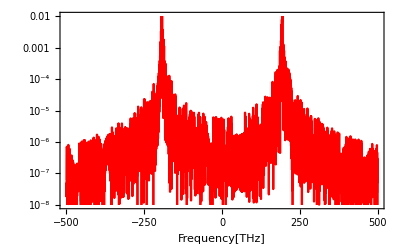

```mathematica
LogPlot[(Re[Cs[f]]^2+Im[Cs[f]]^2),{f,-0.5*10^3,0.5*10^3},Frame->True,FrameLabel->{"Frequency[THz]"},BaseStyle->{Bold,FontSize->15},PlotRange->{10^-8,10^-2},PlotStyle->{Red}]
```

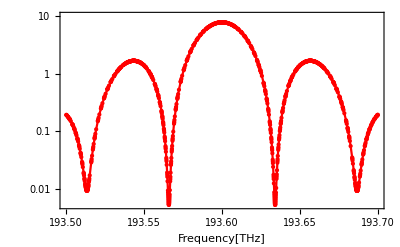

```mathematica
LogPlot[(Re[Cs[f]]^2+Im[Cs[f ]]^2),{f,1.935*10^2,1.937*10^2},Mesh->All,Frame->True,FrameLabel->{"Frequency[THz]"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,10},PlotStyle->{Red}]
```

WolframAlphaQueryNoResults

Cos[1228.36 t]

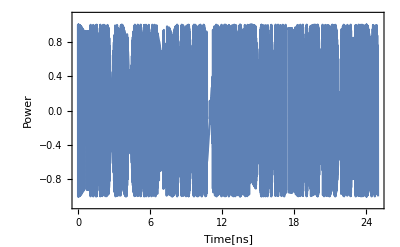

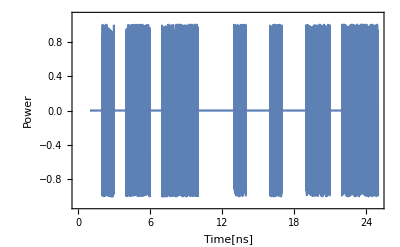

-Graphics-

0.+(9.96828×10^-9 Cos[0.-2563.54 f] Cos[0.+2400.18 f])/(-38220.3+1. f^2)-(9.50153×10^-9 Cos[0.-2563.54 f] Cos[0.+2406.46 f])/(-38220.3+1. f^2)-(9.51522×10^-9 Cos[0.-2563.54 f] Cos[0.+2406.46 f])/(-38220.3+1. f^2)+(9.27541×10^-9 Cos[0.-2563.54 f] Cos[0.+2412.74 f])/(-38220.3+1. f^2)+(9.28856×10^-9 Cos[0.-2563.54 f] Cos[0.+2412.74 f])/(-38220.3+1. f^2)-(8.82291×10^-9 Cos[0.-2563.54 f] Cos[0.+2419.03 f])/(-38220.3+1. f^2)-(8.83551×10^-9 Cos[0.-2563.54 f] Cos[0.+2419.03 f])/(-38220.3+1. f^2)+(8.3704×10^-9 Cos[0.-2563.54 f] Cos[0.+2425.31 f])/(-38220.3+1. f^2)-(8.04259×10^-9 Cos[0.-2563.54 f] Cos[0.+2431.59 f])/(-38220.3+1. f^2)+(7.57858×10^-9 Cos[0.-2563.54 f] Cos[0.+2437.88 f])/(-38220.3+1. f^2)+(7.58954×10^-9 Cos[0.-2563.54 f] Cos[0.+2437.88 f])/(-38220.3+1. f^2)-(7.23927×10^-9 Cos[0.-2563.54 f] Cos[0.+2444.16 f])/(-38220.3+1. f^2)-(6.56996×10^-9 Cos[0.-2563.54 f] Cos[0.+2456.73 f])/(-38220.3+1. f^2)+(6.10814×10^-9 Cos[0.-2563.54 f] Cos[0.+2463.01 f])/(-38220.3+1. f^2)+(5.324×10^-9 Cos[0.-2563.54 f] Cos[0.+2475.58 f])/(-38220.3+1. f^2)-(4.97702×10^-9 Cos[0.-2563.54 f] Cos[0.+2481.86 f])/(-38220.3+1. f^2)+(3.79477×10^-9 Cos[0.-2563.54 f] Cos[0.+2500.71 f])/(-38220.3+1. f^2)-(3.44998×10^-9 Cos[0.-2563.54 f] Cos[0.+2506.99 f])/(-38220.3+1. f^2)-(3.45491×10^-9 Cos[0.-2563.54 f] Cos[0.+2506.99 f])/(-38220.3+1. f^2)+(3.05407×10^-9 Cos[0.-2563.54 f] Cos[0.+2513.27 f])/(-38220.3+1. f^2)+(3.05846×10^-9 Cos[0.-2563.54 f] Cos[0.+2513.27 f])/(-38220.3+1. f^2)-(2.65816×10^-9 Cos[0.-2563.54 f] Cos[0.+2519.56 f])/(-38220.3+1. f^2)+(2.32214×10^-9 Cos[0.-2563.54 f] Cos[0.+2525.84 f])/(-38220.3+1. f^2)-(1.89465×10^-9 Cos[0.-2563.54 f] Cos[0.+2532.12 f])/(-38220.3+1. f^2)-(1.89739×10^-9 Cos[0.-2563.54 f] Cos[0.+2532.12 f])/(-38220.3+1. f^2)+(1.52704×10^-9 Cos[0.-2563.54 f] Cos[0.+2538.41 f])/(-38220.3+1. f^2)-(1.16107×10^-9 Cos[0.-2563.54 f] Cos[0.+2544.69 f])/(-38220.3+1. f^2)+(7.63518×10^-10 Cos[0.-2563.54 f] Cos[0.+2550.97 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2400.18 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2406.46 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2406.46 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2412.74 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2412.74 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2419.03 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2419.03 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2425.31 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2431.59 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2437.88 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2437.88 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2444.16 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2456.73 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2463.01 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2475.58 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2481.86 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2500.71 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2506.99 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2506.99 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2513.27 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2513.27 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2519.56 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2525.84 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.+2532.12 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2532.12 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2538.41 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2544.69 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.+2550.97 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2400.18 f])/(-38220.3+1. f^2)-(9.96828×10^-9 Sin[0.-2563.54 f] Sin[0.+2400.18 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2406.46 f])/(-38220.3+1. f^2)+(9.50153×10^-9 Sin[0.-2563.54 f] Sin[0.+2406.46 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2406.46 f])/(-38220.3+1. f^2)+(9.51522×10^-9 Sin[0.-2563.54 f] Sin[0.+2406.46 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2412.74 f])/(-38220.3+1. f^2)-(9.27541×10^-9 Sin[0.-2563.54 f] Sin[0.+2412.74 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2412.74 f])/(-38220.3+1. f^2)-(9.28856×10^-9 Sin[0.-2563.54 f] Sin[0.+2412.74 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2419.03 f])/(-38220.3+1. f^2)+(8.82291×10^-9 Sin[0.-2563.54 f] Sin[0.+2419.03 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2419.03 f])/(-38220.3+1. f^2)+(8.83551×10^-9 Sin[0.-2563.54 f] Sin[0.+2419.03 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2425.31 f])/(-38220.3+1. f^2)-(8.3704×10^-9 Sin[0.-2563.54 f] Sin[0.+2425.31 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2431.59 f])/(-38220.3+1. f^2)+(8.04259×10^-9 Sin[0.-2563.54 f] Sin[0.+2431.59 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2437.88 f])/(-38220.3+1. f^2)-(7.57858×10^-9 Sin[0.-2563.54 f] Sin[0.+2437.88 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2437.88 f])/(-38220.3+1. f^2)-(7.58954×10^-9 Sin[0.-2563.54 f] Sin[0.+2437.88 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2444.16 f])/(-38220.3+1. f^2)+(7.23927×10^-9 Sin[0.-2563.54 f] Sin[0.+2444.16 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2456.73 f])/(-38220.3+1. f^2)+(6.56996×10^-9 Sin[0.-2563.54 f] Sin[0.+2456.73 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2463.01 f])/(-38220.3+1. f^2)-(6.10814×10^-9 Sin[0.-2563.54 f] Sin[0.+2463.01 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2475.58 f])/(-38220.3+1. f^2)-(5.324×10^-9 Sin[0.-2563.54 f] Sin[0.+2475.58 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2481.86 f])/(-38220.3+1. f^2)+(4.97702×10^-9 Sin[0.-2563.54 f] Sin[0.+2481.86 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2500.71 f])/(-38220.3+1. f^2)-(3.79477×10^-9 Sin[0.-2563.54 f] Sin[0.+2500.71 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2506.99 f])/(-38220.3+1. f^2)+(3.44998×10^-9 Sin[0.-2563.54 f] Sin[0.+2506.99 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2506.99 f])/(-38220.3+1. f^2)+(3.45491×10^-9 Sin[0.-2563.54 f] Sin[0.+2506.99 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2513.27 f])/(-38220.3+1. f^2)-(3.05407×10^-9 Sin[0.-2563.54 f] Sin[0.+2513.27 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2513.27 f])/(-38220.3+1. f^2)-(3.05846×10^-9 Sin[0.-2563.54 f] Sin[0.+2513.27 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2519.56 f])/(-38220.3+1. f^2)+(2.65816×10^-9 Sin[0.-2563.54 f] Sin[0.+2519.56 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2525.84 f])/(-38220.3+1. f^2)-(2.32214×10^-9 Sin[0.-2563.54 f] Sin[0.+2525.84 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Sin[0.+2532.12 f])/(-38220.3+1. f^2)+(1.89465×10^-9 Sin[0.-2563.54 f] Sin[0.+2532.12 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2532.12 f])/(-38220.3+1. f^2)+(1.89739×10^-9 Sin[0.-2563.54 f] Sin[0.+2532.12 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2538.41 f])/(-38220.3+1. f^2)-(1.52704×10^-9 Sin[0.-2563.54 f] Sin[0.+2538.41 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2544.69 f])/(-38220.3+1. f^2)+(1.16107×10^-9 Sin[0.-2563.54 f] Sin[0.+2544.69 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Sin[0.+2550.97 f])/(-38220.3+1. f^2)-(7.63518×10^-10 Sin[0.-2563.54 f] Sin[0.+2550.97 f])/(-38220.3+1. f^2)+ⅈ (0.+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2400.18 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2406.46 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2406.46 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2412.74 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2412.74 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2419.03 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2419.03 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2425.31 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2431.59 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2437.88 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2437.88 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2444.16 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2456.73 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2463.01 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2475.58 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2481.86 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2500.71 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2506.99 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2506.99 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2513.27 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2513.27 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2519.56 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2525.84 f])/(-38220.3+1. f^2)+(0.159155 f Cos[0.-2563.54 f] Cos[0.+2532.12 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2532.12 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2538.41 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2544.69 f])/(-38220.3+1. f^2)-(0.159155 f Cos[0.-2563.54 f] Cos[0.+2550.97 f])/(-38220.3+1. f^2)+(9.96828×10^-9 Cos[0.+2400.18 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(9.50153×10^-9 Cos[0.+2406.46 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(9.51522×10^-9 Cos[0.+2406.46 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(9.27541×10^-9 Cos[0.+2412.74 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(9.28856×10^-9 Cos[0.+2412.74 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(8.82291×10^-9 Cos[0.+2419.03 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(8.83551×10^-9 Cos[0.+2419.03 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(8.3704×10^-9 Cos[0.+2425.31 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(8.04259×10^-9 Cos[0.+2431.59 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(7.57858×10^-9 Cos[0.+2437.88 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(7.58954×10^-9 Cos[0.+2437.88 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(7.23927×10^-9 Cos[0.+2444.16 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(6.56996×10^-9 Cos[0.+2456.73 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(6.10814×10^-9 Cos[0.+2463.01 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(5.324×10^-9 Cos[0.+2475.58 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(4.97702×10^-9 Cos[0.+2481.86 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(3.79477×10^-9 Cos[0.+2500.71 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(3.44998×10^-9 Cos[0.+2506.99 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(3.45491×10^-9 Cos[0.+2506.99 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(3.05407×10^-9 Cos[0.+2513.27 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(3.05846×10^-9 Cos[0.+2513.27 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(2.65816×10^-9 Cos[0.+2519.56 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(2.32214×10^-9 Cos[0.+2525.84 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(1.89465×10^-9 Cos[0.+2532.12 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(1.89739×10^-9 Cos[0.+2532.12 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(1.52704×10^-9 Cos[0.+2538.41 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)-(1.16107×10^-9 Cos[0.+2544.69 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(7.63518×10^-10 Cos[0.+2550.97 f] Sin[0.-2563.54 f])/(-38220.3+1. f^2)+(9.96828×10^-9 Cos[0.-2563.54 f] Sin[0.+2400.18 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2400.18 f])/(-38220.3+1. f^2)-(9.50153×10^-9 Cos[0.-2563.54 f] Sin[0.+2406.46 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2406.46 f])/(-38220.3+1. f^2)-(9.51522×10^-9 Cos[0.-2563.54 f] Sin[0.+2406.46 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2406.46 f])/(-38220.3+1. f^2)+(9.27541×10^-9 Cos[0.-2563.54 f] Sin[0.+2412.74 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2412.74 f])/(-38220.3+1. f^2)+(9.28856×10^-9 Cos[0.-2563.54 f] Sin[0.+2412.74 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2412.74 f])/(-38220.3+1. f^2)-(8.82291×10^-9 Cos[0.-2563.54 f] Sin[0.+2419.03 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2419.03 f])/(-38220.3+1. f^2)-(8.83551×10^-9 Cos[0.-2563.54 f] Sin[0.+2419.03 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2419.03 f])/(-38220.3+1. f^2)+(8.3704×10^-9 Cos[0.-2563.54 f] Sin[0.+2425.31 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2425.31 f])/(-38220.3+1. f^2)-(8.04259×10^-9 Cos[0.-2563.54 f] Sin[0.+2431.59 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2431.59 f])/(-38220.3+1. f^2)+(7.57858×10^-9 Cos[0.-2563.54 f] Sin[0.+2437.88 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2437.88 f])/(-38220.3+1. f^2)+(7.58954×10^-9 Cos[0.-2563.54 f] Sin[0.+2437.88 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2437.88 f])/(-38220.3+1. f^2)-(7.23927×10^-9 Cos[0.-2563.54 f] Sin[0.+2444.16 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2444.16 f])/(-38220.3+1. f^2)-(6.56996×10^-9 Cos[0.-2563.54 f] Sin[0.+2456.73 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2456.73 f])/(-38220.3+1. f^2)+(6.10814×10^-9 Cos[0.-2563.54 f] Sin[0.+2463.01 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2463.01 f])/(-38220.3+1. f^2)+(5.324×10^-9 Cos[0.-2563.54 f] Sin[0.+2475.58 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2475.58 f])/(-38220.3+1. f^2)-(4.97702×10^-9 Cos[0.-2563.54 f] Sin[0.+2481.86 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2481.86 f])/(-38220.3+1. f^2)+(3.79477×10^-9 Cos[0.-2563.54 f] Sin[0.+2500.71 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2500.71 f])/(-38220.3+1. f^2)-(3.44998×10^-9 Cos[0.-2563.54 f] Sin[0.+2506.99 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2506.99 f])/(-38220.3+1. f^2)-(3.45491×10^-9 Cos[0.-2563.54 f] Sin[0.+2506.99 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2506.99 f])/(-38220.3+1. f^2)+(3.05407×10^-9 Cos[0.-2563.54 f] Sin[0.+2513.27 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2513.27 f])/(-38220.3+1. f^2)+(3.05846×10^-9 Cos[0.-2563.54 f] Sin[0.+2513.27 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2513.27 f])/(-38220.3+1. f^2)-(2.65816×10^-9 Cos[0.-2563.54 f] Sin[0.+2519.56 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2519.56 f])/(-38220.3+1. f^2)+(2.32214×10^-9 Cos[0.-2563.54 f] Sin[0.+2525.84 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2525.84 f])/(-38220.3+1. f^2)-(1.89465×10^-9 Cos[0.-2563.54 f] Sin[0.+2532.12 f])/(-38220.3+1. f^2)-(0.159155 f Sin[0.-2563.54 f] Sin[0.+2532.12 f])/(-38220.3+1. f^2)-(1.89739×10^-9 Cos[0.-2563.54 f] Sin[0.+2532.12 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2532.12 f])/(-38220.3+1. f^2)+(1.52704×10^-9 Cos[0.-2563.54 f] Sin[0.+2538.41 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2538.41 f])/(-38220.3+1. f^2)-(1.16107×10^-9 Cos[0.-2563.54 f] Sin[0.+2544.69 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2544.69 f])/(-38220.3+1. f^2)+(7.63518×10^-10 Cos[0.-2563.54 f] Sin[0.+2550.97 f])/(-38220.3+1. f^2)+(0.159155 f Sin[0.-2563.54 f] Sin[0.+2550.97 f])/(-38220.3+1. f^2))

```mathematica
Fc2= 195.5 ;(*搬送波の周波数[THz]*)
carrier2[t_]= Cos[2*Pi*Fc2*t]
Plot[carrier2[t], {t,0,25},Frame->True,FrameLabel->{"Time[ns]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
cs2[t_]:=signal[t]*carrier2[t]

Plot[Evaluate[cs2[t]],{t,1,bit},Frame->True,FrameLabel->{"Time[ns]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
Plot[Evaluate[cs2[t]],{t,1,bit},Frame->True,FrameLabel->{"Time[ns]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
ComplexExpand[∫_0^(bit*25) cs2[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]
```

```mathematica
Evaluate[∫_0^bit cs2[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]
ComplexExpand[Integratepaclet:ref/Integrate[cs2[t1]*ⅇ^(-ⅈ*2*Pi*f*t1),{t,0,25}]]
Nintegrate[cs2[t1]*ⅇ^(-ⅈ*2*Pi*f*t1),{t,0,25}]
```

1/(-38220.3+1. f^2)ⅇ^((0.-2243.1 ⅈ) f) (ⅇ^((0.+2086.02 ⅈ) f) (-9.51522×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2098.58 ⅈ) f) (-8.83551×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2111.15 ⅈ) f) (-8.04259×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2136.28 ⅈ) f) (-6.56996×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2186.55 ⅈ) f) (-3.45491×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2211.68 ⅈ) f) (-1.89739×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2224.25 ⅈ) f) (-1.16107×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2230.53 ⅈ) f) (7.63518×10^-10-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2217.96 ⅈ) f) (1.52704×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2192.83 ⅈ) f) (3.05407×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2142.57 ⅈ) f) (6.10814×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2117.43 ⅈ) f) (7.57858×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2104.87 ⅈ) f) (8.3704×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2092.3 ⅈ) f) (9.27541×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2098.58 ⅈ) f) (-8.82291×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2123.72 ⅈ) f) (-7.23927×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2161.42 ⅈ) f) (-4.97702×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2186.55 ⅈ) f) (-3.44998×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2199.11 ⅈ) f) (-2.65816×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2211.68 ⅈ) f) (-1.89465×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2205.4 ⅈ) f) (2.32214×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2192.83 ⅈ) f) (3.05846×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2180.27 ⅈ) f) (3.79477×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2155.13 ⅈ) f) (5.324×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2117.43 ⅈ) f) (7.58954×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2092.3 ⅈ) f) (9.28856×10^-9+(0.+0.159155 ⅈ) f))

Rule::rhs: パターンpaclet:ref/Integrateは規則System`ComplexExpandDump`reimexpr[«1»]→{RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) «1» (If[1<t1<2,0,0]+If[2<t1<3,1,0]+If[3<t1<4,0,0]+If[4<t1<5,1,0]+If[5<t1<6,1,0]+If[6<t1<7,0,0]+If[7<t1<8,1,0]+If[8<t1<9,1,0]+If[9<t1<10,1,0]+If[10<t1<11,0,0]+«15»),«1»],0}の右辺にあります．

RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) Cos[1228.36 t1] (If[1<t1<2,0,0]+If[2<t1<3,1,0]+If[3<t1<4,0,0]+If[4<t1<5,1,0]+If[5<t1<6,1,0]+If[6<t1<7,0,0]+If[7<t1<8,1,0]+If[8<t1<9,1,0]+If[9<t1<10,1,0]+If[10<t1<11,0,0]+If[11<t1<12,0,0]+If[12<t1<13,0,0]+If[13<t1<14,1,0]+If[14<t1<15,0,0]+If[15<t1<16,0,0]+If[16<t1<17,1,0]+If[17<t1<18,0,0]+If[18<t1<19,0,0]+If[19<t1<20,1,0]+If[20<t1<21,1,0]+If[21<t1<22,0,0]+If[22<t1<23,1,0]+If[23<t1<24,1,0]+If[24<t1<25,1,0]+If[25<t1<26,1,0]),{t,0,25}]

Nintegrate[ⅇ^(-2 ⅈ f π t1) Cos[1228.36 t1] (If[1<t1<2,0,0]+If[2<t1<3,1,0]+If[3<t1<4,0,0]+If[4<t1<5,1,0]+If[5<t1<6,1,0]+If[6<t1<7,0,0]+If[7<t1<8,1,0]+If[8<t1<9,1,0]+If[9<t1<10,1,0]+If[10<t1<11,0,0]+If[11<t1<12,0,0]+If[12<t1<13,0,0]+If[13<t1<14,1,0]+If[14<t1<15,0,0]+If[15<t1<16,0,0]+If[16<t1<17,1,0]+If[17<t1<18,0,0]+If[18<t1<19,0,0]+If[19<t1<20,1,0]+If[20<t1<21,1,0]+If[21<t1<22,0,0]+If[22<t1<23,1,0]+If[23<t1<24,1,0]+If[24<t1<25,1,0]+If[25<t1<26,1,0]),{t,0,25}]

```mathematica
Cs2[f]=ComplexExpand[FourierTransform[cs2[t],t,2*Pi*f]]
```

(3.046×10^-10 Cos[12.5664 f])/(-38220.3+f^2)-(4.632×10^-10 Cos[18.8496 f])/(-38220.3+f^2)+(6.09199×10^-10 Cos[25.1327 f])/(-38220.3+f^2)-(7.56947×10^-10 Cos[31.4159 f])/(-38220.3+f^2)-(7.55854×10^-10 Cos[31.4159 f])/(-38220.3+f^2)+(9.264×10^-10 Cos[37.6991 f])/(-38220.3+f^2)-(1.06045×10^-9 Cos[43.9823 f])/(-38220.3+f^2)+(1.22015×10^-9 Cos[50.2655 f])/(-38220.3+f^2)+(1.2184×10^-9 Cos[50.2655 f])/(-38220.3+f^2)-(1.37831×10^-9 Cos[56.5487 f])/(-38220.3+f^2)-(1.37634×10^-9 Cos[56.5487 f])/(-38220.3+f^2)+(1.51389×10^-9 Cos[62.8319 f])/(-38220.3+f^2)-(1.98554×10^-9 Cos[81.6814 f])/(-38220.3+f^2)+(2.12397×10^-9 Cos[87.9646 f])/(-38220.3+f^2)+(2.4368×10^-9 Cos[100.531 f])/(-38220.3+f^2)-(2.62104×10^-9 Cos[106.814 f])/(-38220.3+f^2)-(2.88805×10^-9 Cos[119.381 f])/(-38220.3+f^2)+(3.02779×10^-9 Cos[125.664 f])/(-38220.3+f^2)+(3.02342×10^-9 Cos[125.664 f])/(-38220.3+f^2)-(3.20853×10^-9 Cos[131.947 f])/(-38220.3+f^2)+(3.33931×10^-9 Cos[138.23 f])/(-38220.3+f^2)-(3.52486×10^-9 Cos[144.513 f])/(-38220.3+f^2)-(3.51983×10^-9 Cos[144.513 f])/(-38220.3+f^2)+(3.7056×10^-9 Cos[150.796 f])/(-38220.3+f^2)+(3.70035×10^-9 Cos[150.796 f])/(-38220.3+f^2)-(3.79603×10^-9 Cos[157.08 f])/(-38220.3+f^2)-(3.79056×10^-9 Cos[157.08 f])/(-38220.3+f^2)+(3.97677×10^-9 Cos[163.363 f])/(-38220.3+f^2)-(0.0634936 f Sin[12.5664 f])/(-38220.3+f^2)-(0.0634936 f Sin[18.8496 f])/(-38220.3+f^2)-(0.0634936 f Sin[25.1327 f])/(-38220.3+f^2)-(0.0634936 f Sin[31.4159 f])/(-38220.3+f^2)+(0.0634936 f Sin[31.4159 f])/(-38220.3+f^2)+(0.0634936 f Sin[37.6991 f])/(-38220.3+f^2)+(0.0634936 f Sin[43.9823 f])/(-38220.3+f^2)+(0.0634936 f Sin[50.2655 f])/(-38220.3+f^2)-(0.0634936 f Sin[50.2655 f])/(-38220.3+f^2)-(0.0634936 f Sin[56.5487 f])/(-38220.3+f^2)+(0.0634936 f Sin[56.5487 f])/(-38220.3+f^2)+(0.0634936 f Sin[62.8319 f])/(-38220.3+f^2)+(0.0634936 f Sin[81.6814 f])/(-38220.3+f^2)+(0.0634936 f Sin[87.9646 f])/(-38220.3+f^2)-(0.0634936 f Sin[100.531 f])/(-38220.3+f^2)-(0.0634936 f Sin[106.814 f])/(-38220.3+f^2)+(0.0634936 f Sin[119.381 f])/(-38220.3+f^2)+(0.0634936 f Sin[125.664 f])/(-38220.3+f^2)-(0.0634936 f Sin[125.664 f])/(-38220.3+f^2)-(0.0634936 f Sin[131.947 f])/(-38220.3+f^2)-(0.0634936 f Sin[138.23 f])/(-38220.3+f^2)-(0.0634936 f Sin[144.513 f])/(-38220.3+f^2)+(0.0634936 f Sin[144.513 f])/(-38220.3+f^2)+(0.0634936 f Sin[150.796 f])/(-38220.3+f^2)-(0.0634936 f Sin[150.796 f])/(-38220.3+f^2)-(0.0634936 f Sin[157.08 f])/(-38220.3+f^2)+(0.0634936 f Sin[157.08 f])/(-38220.3+f^2)+(0.0634936 f Sin[163.363 f])/(-38220.3+f^2)+ⅈ ((0.0634936 f Cos[12.5664 f])/(-38220.3+f^2)+(0.0634936 f Cos[18.8496 f])/(-38220.3+f^2)+(0.0634936 f Cos[25.1327 f])/(-38220.3+f^2)+(0.0634936 f Cos[31.4159 f])/(-38220.3+f^2)-(0.0634936 f Cos[31.4159 f])/(-38220.3+f^2)-(0.0634936 f Cos[37.6991 f])/(-38220.3+f^2)-(0.0634936 f Cos[43.9823 f])/(-38220.3+f^2)-(0.0634936 f Cos[50.2655 f])/(-38220.3+f^2)+(0.0634936 f Cos[50.2655 f])/(-38220.3+f^2)+(0.0634936 f Cos[56.5487 f])/(-38220.3+f^2)-(0.0634936 f Cos[56.5487 f])/(-38220.3+f^2)-(0.0634936 f Cos[62.8319 f])/(-38220.3+f^2)-(0.0634936 f Cos[81.6814 f])/(-38220.3+f^2)-(0.0634936 f Cos[87.9646 f])/(-38220.3+f^2)+(0.0634936 f Cos[100.531 f])/(-38220.3+f^2)+(0.0634936 f Cos[106.814 f])/(-38220.3+f^2)-(0.0634936 f Cos[119.381 f])/(-38220.3+f^2)-(0.0634936 f Cos[125.664 f])/(-38220.3+f^2)+(0.0634936 f Cos[125.664 f])/(-38220.3+f^2)+(0.0634936 f Cos[131.947 f])/(-38220.3+f^2)+(0.0634936 f Cos[138.23 f])/(-38220.3+f^2)+(0.0634936 f Cos[144.513 f])/(-38220.3+f^2)-(0.0634936 f Cos[144.513 f])/(-38220.3+f^2)-(0.0634936 f Cos[150.796 f])/(-38220.3+f^2)+(0.0634936 f Cos[150.796 f])/(-38220.3+f^2)+(0.0634936 f Cos[157.08 f])/(-38220.3+f^2)-(0.0634936 f Cos[157.08 f])/(-38220.3+f^2)-(0.0634936 f Cos[163.363 f])/(-38220.3+f^2)+(3.046×10^-10 Sin[12.5664 f])/(-38220.3+f^2)-(4.632×10^-10 Sin[18.8496 f])/(-38220.3+f^2)+(6.09199×10^-10 Sin[25.1327 f])/(-38220.3+f^2)-(7.56947×10^-10 Sin[31.4159 f])/(-38220.3+f^2)-(7.55854×10^-10 Sin[31.4159 f])/(-38220.3+f^2)+(9.264×10^-10 Sin[37.6991 f])/(-38220.3+f^2)-(1.06045×10^-9 Sin[43.9823 f])/(-38220.3+f^2)+(1.22015×10^-9 Sin[50.2655 f])/(-38220.3+f^2)+(1.2184×10^-9 Sin[50.2655 f])/(-38220.3+f^2)-(1.37831×10^-9 Sin[56.5487 f])/(-38220.3+f^2)-(1.37634×10^-9 Sin[56.5487 f])/(-38220.3+f^2)+(1.51389×10^-9 Sin[62.8319 f])/(-38220.3+f^2)-(1.98554×10^-9 Sin[81.6814 f])/(-38220.3+f^2)+(2.12397×10^-9 Sin[87.9646 f])/(-38220.3+f^2)+(2.4368×10^-9 Sin[100.531 f])/(-38220.3+f^2)-(2.62104×10^-9 Sin[106.814 f])/(-38220.3+f^2)-(2.88805×10^-9 Sin[119.381 f])/(-38220.3+f^2)+(3.02779×10^-9 Sin[125.664 f])/(-38220.3+f^2)+(3.02342×10^-9 Sin[125.664 f])/(-38220.3+f^2)-(3.20853×10^-9 Sin[131.947 f])/(-38220.3+f^2)+(3.33931×10^-9 Sin[138.23 f])/(-38220.3+f^2)-(3.52486×10^-9 Sin[144.513 f])/(-38220.3+f^2)-(3.51983×10^-9 Sin[144.513 f])/(-38220.3+f^2)+(3.7056×10^-9 Sin[150.796 f])/(-38220.3+f^2)+(3.70035×10^-9 Sin[150.796 f])/(-38220.3+f^2)-(3.79603×10^-9 Sin[157.08 f])/(-38220.3+f^2)-(3.79056×10^-9 Sin[157.08 f])/(-38220.3+f^2)+(3.97677×10^-9 Sin[163.363 f])/(-38220.3+f^2))

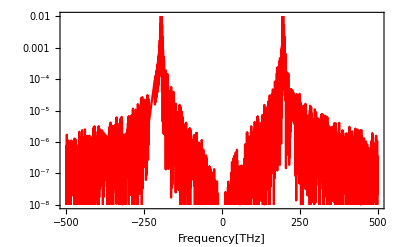

```mathematica
LogPlot[(Re[Cs2[f]]^2+Im[Cs2[f]]^2),{f,-0.5*10^3,0.5*10^3},Frame->True,FrameLabel->{"Frequency[THz]"},BaseStyle->{Bold,FontSize->15},PlotRange->{10^-8,10^-2},PlotStyle->{Red}]
```

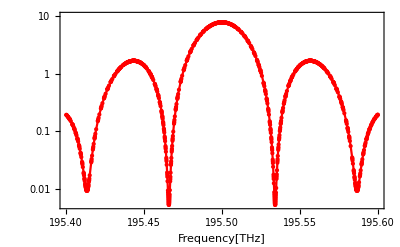

```mathematica
LogPlot[(Re[Cs2[f]]^2+Im[Cs2[f ]]^2),{f,1.954*10^2,1.956*10^2},Mesh->All,Frame->True,FrameLabel->{"Frequency[THz]"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,10},PlotStyle->{Red}]
```

```mathematica
∫_0^bit cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

1/(-37481.+1. f^2)ⅇ^((0.-2243.1 ⅈ) f) (ⅇ^((0.+2098.58 ⅈ) f) (29.3043+(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2104.87 ⅈ) f) (29.3043-(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2192.83 ⅈ) f) (29.3043+(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2199.11 ⅈ) f) (29.3043-(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2224.25 ⅈ) f) (29.3043+(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2230.53 ⅈ) f) (29.3043-(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2192.83 ⅈ) f) (-29.3043-(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2161.42 ⅈ) f) (-29.3043-(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2136.28 ⅈ) f) (-29.3043+(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2098.58 ⅈ) f) (-29.3043-(0.+0.0491816 ⅈ) f)+ⅇ^((0.+2092.3 ⅈ) f) (-18.1111-(0.+0.128759 ⅈ) f)+ⅇ^((0.+2142.57 ⅈ) f) (-18.1111+(0.+0.128759 ⅈ) f)+ⅇ^((0.+2155.13 ⅈ) f) (-18.1111-(0.+0.128759 ⅈ) f)+ⅇ^((0.+2186.55 ⅈ) f) (-18.1111-(0.+0.128759 ⅈ) f)+ⅇ^((0.+2217.96 ⅈ) f) (18.1111+(0.+0.128759 ⅈ) f)+ⅇ^((0.+2205.4 ⅈ) f) (18.1111-(0.+0.128759 ⅈ) f)+ⅇ^((0.+2186.55 ⅈ) f) (18.1111+(0.+0.128759 ⅈ) f)+ⅇ^((0.+2123.72 ⅈ) f) (18.1111+(0.+0.128759 ⅈ) f)+ⅇ^((0.+2111.15 ⅈ) f) (18.1111-(0.+0.128759 ⅈ) f)+ⅇ^((0.+2092.3 ⅈ) f) (18.1111+(0.+0.128759 ⅈ) f)+ⅇ^((0.+2211.68 ⅈ) f) (1.87904×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2117.43 ⅈ) f) (7.51616×10^-9-(0.+0.159155 ⅈ) f)+ⅇ^((0.+2211.68 ⅈ) f) (1.87614×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2180.27 ⅈ) f) (3.75227×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2117.43 ⅈ) f) (7.50455×10^-9+(0.+0.159155 ⅈ) f)+ⅇ^((0.+2086.02 ⅈ) f) (9.32464×10^-9+(0.+0.159155 ⅈ) f))

```mathematica
fc[f_]:=1/(-37480.96000000001+1. f^2)ⅇ^((0.-2243.0971546631113 ⅈ) f) (ⅇ^((0.+2098.5838925979824 ⅈ) f) (29.30433093562274+(0.+0.04918158211194266 ⅈ) f)+ⅇ^((0.+2104.8670779051595 ⅈ) f) (29.304330935514205-(0.+0.04918158211366812 ⅈ) f)+ⅇ^((0.+2192.831672205675 ⅈ) f) (29.304330933883463+(0.+0.049181582139592124 ⅈ) f)+ⅇ^((0.+2199.114857512854 ⅈ) f) (29.304330933772228-(0.+0.049181582141360376 ⅈ) f)+ⅇ^((0.+2224.2475987415723 ⅈ) f) (29.3043309333167+(0.+0.049181582148602104 ⅈ) f)+ⅇ^((0.+2230.5307840487517 ⅈ) f) (29.30433093319591-(0.+0.049181582150522304 ⅈ) f)+ⅇ^((0.+2192.8316722056743 ⅈ) f) (-29.30433093204759-(0.+0.0491815821687773 ⅈ) f)+ⅇ^((0.+2161.4157456697762 ⅈ) f) (-29.304330931466932-(0.+0.04918158217800806 ⅈ) f)+ⅇ^((0.+2136.28300444106 ⅈ) f) (-29.304330930984666+(0.+0.04918158218567457 ⅈ) f)+ⅇ^((0.+2098.5838925979797 ⅈ) f) (-29.304330930288305-(0.+0.049181582196744886 ⅈ) f)+ⅇ^((0.+2092.300707290803 ⅈ) f) (-18.111072541488035-(0.+0.12875905367257548 ⅈ) f)+ⅇ^((0.+2142.5661897482373 ⅈ) f) (-18.111072538958208+(0.+0.1287590536820694 ⅈ) f)+ⅇ^((0.+2155.1325603625983 ⅈ) f) (-18.111072538361693-(0.+0.128759053684308 ⅈ) f)+ⅇ^((0.+2186.548486898496 ⅈ) f) (-18.11107253688921-(0.+0.12875905368983395 ⅈ) f)+ⅇ^((0.+2217.9644134343926 ⅈ) f) (18.111072532945517+(0.+0.12875905370463386 ⅈ) f)+ⅇ^((0.+2205.398042820034 ⅈ) f) (18.11107253231306-(0.+0.12875905370700733 ⅈ) f)+ⅇ^((0.+2186.5484868984945 ⅈ) f) (18.11107253140267+(0.+0.12875905371042387 ⅈ) f)+ⅇ^((0.+2123.7166338266984 ⅈ) f) (18.11107252840766+(0.+0.12875905372166352 ⅈ) f)+ⅇ^((0.+2111.1502632123415 ⅈ) f) (18.111072527782255-(0.+0.12875905372401056 ⅈ) f)+ⅇ^((0.+2092.3007072908 ⅈ) f) (18.1110725267968+(0.+0.1287590537277088 ⅈ) f)+ⅇ^((0.+2211.6812281272128 ⅈ) f) (1.879040739720117*^-9-(0.+0.15915494309189535 ⅈ) f)+ⅇ^((0.+2117.4334485195186 ⅈ) f) (7.516162958880468*^-9-(0.+0.15915494309189535 ⅈ) f)+ⅇ^((0.+2211.6812281272137 ⅈ) f) (1.8761366420950264*^-9+(0.+0.15915494309189535 ⅈ) f)+ⅇ^((0.+2180.265301591316 ⅈ) f) (3.752273284190053*^-9+(0.+0.15915494309189535 ⅈ) f)+ⅇ^((0.+2117.4334485195213 ⅈ) f) (7.504546568380106*^-9+(0.+0.15915494309189535 ⅈ) f)+ⅇ^((0.+2086.0175219836233 ⅈ) f) (9.324635786865952*^-9+(0.+0.15915494309189535 ⅈ) f))
```

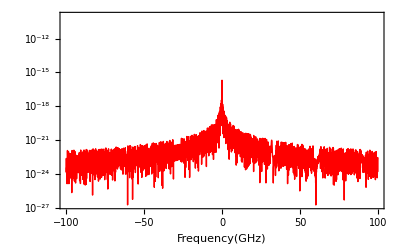

```mathematica
LogPlot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-100,100},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(GHz)"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,10^-10}]
```

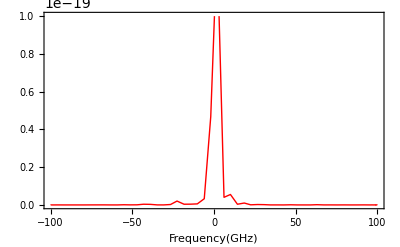

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-100,100},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(GHz)"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,100*10^-21}]
```

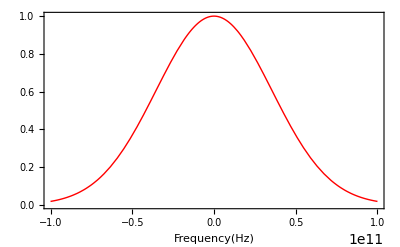

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->12}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-12],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

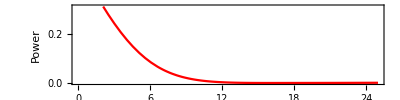

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->12,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->400]
```